# Exploring Surveys - Student Notebook

In this module, students design a survey, administer the survey to their peers, and analyse the results, curating useful data visualisations and descriptive statistics .

Learning Objective

Students will be able to understand the advantages and disadvantages of different types of data, and select appropriate visualizations and descriptive statistics to describe their data.

## STARTING POINT

“The goal of today’s class is to create a survey, gather responses, and analyse your data.”

```mathematica
bin=CreateDatabin[]
```

```mathematica
CloudDeploy[
FormFunction[{
{"name","What is your name?"}->"String",
{"age","How old are you?"}->"Number",
{"gender", "What is your gender?"} -> {"Male","Female","Other"},
{"height","How tall are you in cm?" }-> "Number",
{"weight","How much do you weigh in lbs?" }-> "Number",
{"exercise", "How many minutes of exercise do you do a day?"}->"Number",
{"water","How many glasses of water did you drink yesterday?"} -> "Number",{"pets", "How many pets do you own?"}->"Number",
{"health", "How healthy do you feel?"} -> {"Very Unhealthy","Unhealthy","Healthy","Very Healthy"}
},
DatabinAdd[bin,<|"name"->#name ,"age"->#age, "gender" ->#gender, "height" ->#height, "weight" ->#weight, "exercise" ->#exercise, "water" ->#water, "pets" ->#pets, "health" -> #health|>]&],
Permissions -> "Public"]
```

◼  Try using the documentation for Control Objects to write a question using a slider or radio buttons

CHECKPOINT

Create a databin, figure out how questions are added or changed, and make or change at least one question.

“Let’s work on filling out each other’s surveys.”

CHECKPOINT

Gather at least 10 responses to your survey, and help other people by filling in their survey too.

“Now we have data, let’s create some visualisations”

You’ve successfully gathered some responses to your survey! Can you remember how to look at all the data in the databin?

Now that we have data, we want to make some visualizations and learn more about our data. Experiment with this tool, and see what types of visualization you can make.

```mathematica
keys=Drop[Keys[Last[Normal[Dataset[bin]]]],-1];
val=Drop[(Values[bin][#1]&)/@Keys[Last[Normal[Dataset[bin]]]],-1];

DynamicModule[
{x,y,type,plotTypes, h=1,stats},
plotTypes[type_String,y_]:=
Which[
type=="Histogram",
Which[
NumberQ[Last[val⟦y⟧]],Column[{stats[x],Row[{Tooltip["How wide would you like your histogram bins to be? ","Try making the bins larger or smaller, and see how it helps you to visualize the data"],InputField[Dynamic[h],FieldSize->2]}],Histogram[val⟦y⟧,{h},PlotLabel->"Histogram of" keys[[y]],ImageSize->500,ImagePadding->{{30,30},{30,30}}]}],
StringQ[Last[val⟦y⟧]],
BarChart[Counts[val⟦y⟧], PlotLabel->"Histogram of" keys[[y]],ChartLabels->Automatic,ImageSize->500,ImagePadding->{{30,30},{30,30}}]],
type=="Box and Whisker",
Which[
NumberQ[Last[val⟦y⟧]],Column[{stats[x],BoxWhiskerChart[val⟦y⟧,"Outliers",PlotLabel->"Box and Whisker Chart of" keys[[y]],ImageSize->500,ImagePadding->{{30,30},{30,30}}]}],
StringQ[Last[val⟦y⟧]],"We can't make a Box and Whisker Plot with non-numeric data, try a different plot"],type=="Pie Chart",
PieChart[Counts[val⟦y⟧],PlotLabel->"Pie Chart of" keys[[y]],ChartLabels->Automatic,ImageSize->500,ImagePadding->{{30,30},{30,30}}]];
Column[
{TabView[AssociationThread[keys->val],Dynamic[x],Alignment->Center],SetterBar[Dynamic[type],{"Histogram","Box and Whisker","Pie Chart"}],Dynamic[plotTypes[type,x]]}],
Initialization:>(stats[x_] := Column[{Tooltip[Style["Measuring the Location Statistics of the Data","Subsubtitle"],"Location Statistics, or Central Tendency, means looking at the middle of the data. These measurments are commenly known as averages"],Tooltip["Mean = " Dynamic[N[Mean[val⟦x⟧],3]],"The mean is the average: we calculate it by adding all the data points together and dividing that by the number of data points there are"],Tooltip["Median = " Dynamic[N[Median[val⟦x⟧],3]],"The median is the middle number: we calculate this by putting all the data points in order and finding the one in the middle"],Tooltip["Modes = " Dynamic[Commonest[val⟦x⟧]],"The mode is the most common number in a data set"],Tooltip[Style["Measuring the Dispersion of the Data","Subsubtitle"],"Measuring the dispersion, or spread, means that we can see how varied or diverse the data is"],Tooltip["Range = " Dynamic[Abs[Max[val⟦x⟧]-Min[val⟦x⟧]]],"The range is the difference between the biggest and the smallest data point"],Tooltip["Interquartile Range = " Dynamic[N[InterquartileRange[val⟦x⟧],3]],"The interquartile range is the difference between the 75% percentile and the 25% percentile data points. This is useful because we are ignoring all the outliers"],"Number of Responses = " Dynamic[Length[val⟦x⟧]]}
])
]
```

◼  Are there some charts that are more useful than others for different types of data? Which chart was the least helpful and the most helpful for understanding your data?

◼  What happens when you change the width of the bins in your histogram?

◼  What is the point of creating visualizations and looking at descriptive statistics? Why not just look at the data itself?

CHECKPOINT

Check that students understand the concept of having different types of data (continuous, discreet and categoric), and good ways of visualizing the different types.

“What can we find out using this data?”

Alongside the charts and graphs, there was also some information about the data written in numbers. These are called Descriptive Statistics. You can find out a lot about your data by looking at the Descriptive Statistics.

◼  What’s the difference between the Mean, Median, and Mode?

◼  Why do we care about the dispersion of the data?

Now that we’ ve explored the data, our next goal is to come up with a series of hypotheses, or predictions, about the data. Did you notice any patterns in your data?

◼  What other ways can you think of for displaying two sets of data?

CHECKPOINT

Come up with at least one hypothesis about your data, and use some charts or Descriptive Statistics to give evidence for or against your hypothesis

“We want to be able to show other people what we’ve discovered about our data.”

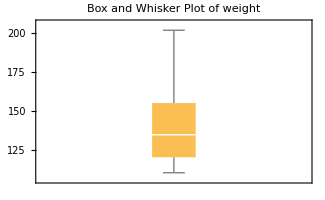
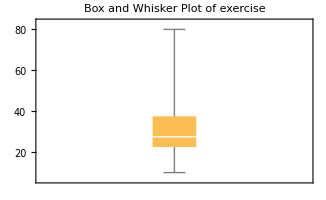
You can use this space to gather up the most useful charts and descriptive statistics which give evidence for or against your hypotheses. Here’s an example:

Hypothesis: The distribution of ‘weight’ and ‘minutes of exercise’ is similar

-Graphics--Graphics-

Descriptive Statistics:

Weight:
Range = 
Interquartile Range = 

Exercise:
Range = 
Interquartile Range =  

Explanation:
From these graphs and statistics, we can see that both weight and exercise have a wide range. Exercise has a smaller interquartile range, which shows that the people who responded have more similar exercise habits than weight. For both weight and exercise, there are people who responded much higher than the average.
From this, we can see that the distribution of weight and minutes of exercise is fairly similar, but it is not the same.

◼  Why do we use data visualizations instead of just showing the data?

◼  Why do some charts explain/describe the data better than others?

### Possible Additional Relevant Functions

ListLinePlot• ListPlot • AssociationThread • Correlation • StandardDeviation • Variance • Skewness